```mathematica
Remove[κ,Γpurcell,χdisp]
```

```mathematica
Γpurcell[κ_,gqr_,Δ_] := κ*gqr^2/(Δ^2+(κ/2)^2);
Γpurcell2[κ_,gqr_,Δ_] := κ*gqr^2/(Δ^2);
χdisp[Δ_,gqr_] := gqr^2/Δ;
```

```mathematica
Δχ[χ_,g_]:=g^2/χ;
Δp[Γ_,κ_,g_]:=Sqrt[κ*g^2/Γ-(κ/2)^2]
```

```mathematica
ContourPlot[Δχ[1/T,2π*10,g],{T,1,10},{g,0,200},ContourLabels->Function[{x,y,z},Text[Framed["Δ="<>ToString[z]],{x-1,y+2},Background->White]],BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"T_Purcell [μs]","g [MHz]"},PlotRange->Full]
```

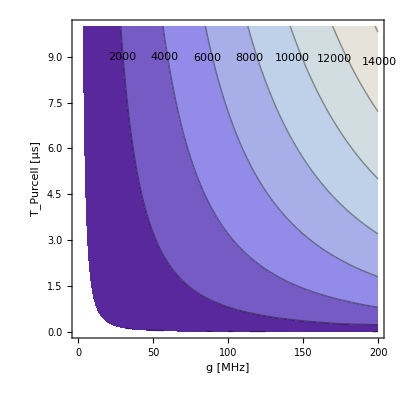

```mathematica
ContourPlot[Δp[1/T,500,g],{g,0,200},{T,0,10},ContourLabels->Function[{x,y,z},Text[Framed[ToString[z]],{x+1,y-1},Background->White]],BaseStyle->{FontSize->16},Frame->{True,True,False,False},FrameLabel->{"g [MHz]","T_Purcell [μs]"},PlotRange->Full]
```

```mathematica
(2.π*7*10*^9/1000.)
```

4.39823×10^8

```mathematica
Δs={0.1,0.2,0.5,1,2,4,8,16};
```

```mathematica
Γpurcell2[κ,g,Δ*g]/κ
```

1/Δ^2

```mathematica
χdisp[Δ*g,g]
```

g/Δ

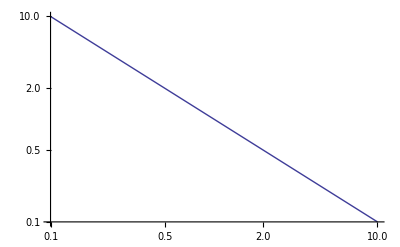

```mathematica
LogLogPlot[χdisp[Δ*g,g]/g,{Δ,0.1,10}]
```

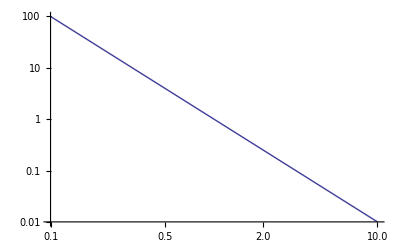

```mathematica
LogLogPlot[Γpurcell2[κ,g,Δ*g]/κ,{Δ,0.1,10}]
```

```mathematica
purcelldatadelta=Map[Block[{Δ=#},{Δ,Γpurcell[0.5,1,#]}]&,Range[0.01,0.2,0.001]];
Export[NotebookDirectory[]<>"purcell_vs_delta_over_g.csv",purcelldata]
```

```mathematica
purcelldata=Map[Block[{g=#},Flatten[{g,Map[1/Γpurcell[0.5,g,#]&,Δs]}]]&,Range[0.01,0.2,0.001]];
Export[NotebookDirectory[]<>"purcell_vs_g_for_fixed_delta.csv",purcelldata]
```

```mathematica
wp1= {gqr->0.05};
```

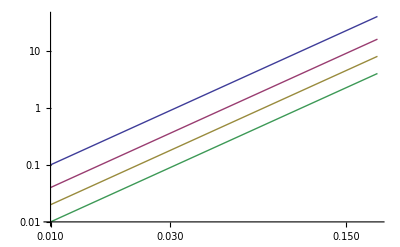

```mathematica
LogLogPlot[{Δχ[0.001,g],Δχ[0.0025,g],Δχ[0.005,g],Δχ[0.01,g]},{g,0.01,0.2}]
```

```mathematica
chidata=Map[Block[{g=#},Flatten[{g,Map[χdisp[#,g]&,Δs]}]]&,Range[0.01,0.2,0.001]];
Export[NotebookDirectory[]<>"chi_vs_g_for_fixed_delta.csv",chidata]
```

E:\cygwin\home\adewes\thesis\material\mathematica\chi_vs_g_for_fixed_delta.csv

```mathematica
isochidata=Map[Block[{g=#},{g,Δχ[0.001,g],Δχ[0.0025,g],Δχ[0.005,g],Δχ[0.01,g]}]&,Range[0.01,0.2,0.001]];
```

```mathematica
Export[NotebookDirectory[]<>"delta_vs_g_for_fixed_chi.csv",isochidata]
```

E:\cygwin\home\adewes\thesis\material\mathematica\delta_vs_g_for_fixed_chi.csv

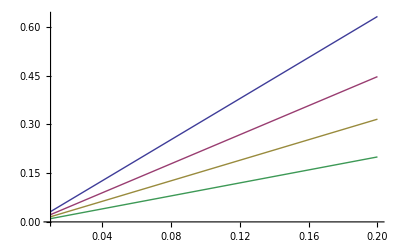

```mathematica
Plot[{Δp[1/(10000),1./1000,g],Δp[1/(5000),1./1000,g],Δp[1/(2500),1./1000,g],Δp[1/(1000),1./1000,g]},{g,0.01,0.2}]
```

```mathematica
isopurcelldata=Map[Block[{g=#},{g,Δp[1/(10000),1./1000,g],Δp[1/(5000),1./1000,g],Δp[1/(2500),1./1000,g],Δp[1/(1000),1./1000,g]}]&,Range[0.01,0.2,0.001]];
```

```mathematica
Export[NotebookDirectory[]<>"delta_vs_g_for_fixed_purcell.csv",isopurcelldata]
```

E:\cygwin\home\adewes\thesis\material\mathematica\delta_vs_g_for_fixed_purcell.csv

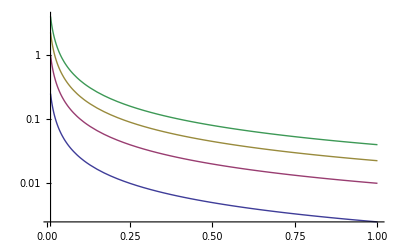

```mathematica
LogPlot[ {χdisp[Δ,0.05],χdisp[Δ,0.1],χdisp[Δ,0.15],χdisp[Δ,0.2]},{Δ,0.01,1},PlotRange->Full]
```

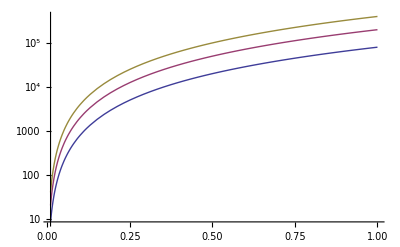

```mathematica
LogPlot[{1/Γpurcell[1/200.,0.05],1/Γpurcell[1/500.,0.05],1/Γpurcell[1/1000.,0.05]} ,{Δ,0.01,1},PlotRange->Full]
```

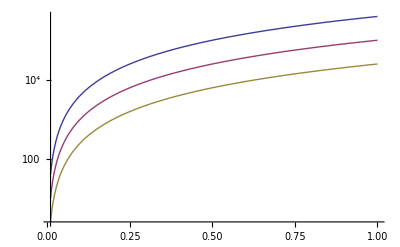

```mathematica
LogPlot[{1/Γpurcell[1/1000.,0.05],1/Γpurcell[1/1000.,0.1],1/Γpurcell[1/1000.,0.2]} ,{Δ,0.01,1},PlotRange->Full]
```

```mathematica
-0.05^2/0.5
```

-0.005

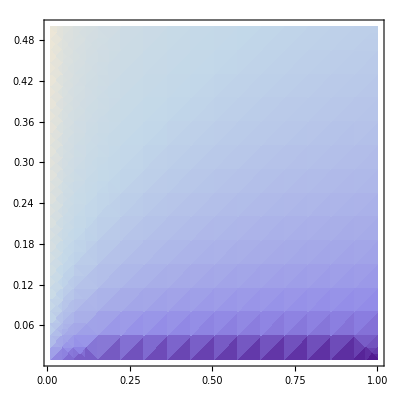

```mathematica
DensityPlot[Log[χdisp[Δ,g]],{Δ,0.01,1},{g,0.01,0.5},PlotRange->Full]
```